## Data Import

Set this to wherever this file is.

```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/Calculations/Angular Momentum/"]
```

/afs/reed.edu/user/e/m/emcmanis/Thesis/Calculations/Angular Momentum

```mathematica
l0=Import["l0.csv"];
l1=Import["l1.csv"];
l2=Import["l2.csv"];
l3=Import["l3.csv"];
l4=Import["l4.csv"];
l5=Import["l5.csv"];
l6=Import["l6.csv"];
l7=Import["l7.csv"];
l8=Import["l8.csv"];
l9=Import["l9.csv"];
l10=Import["l10.csv"];
```

```mathematica
ls={l0,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10};
```

```mathematica
lsplot=Table[Table[{j,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}];
```

There are three data points missing here, as evidenced by the discontinuities in the curves. Instead of going back and taking these data points, I merely shifted the other data points one forward, to make the curves smooth again. The following loop does this.

```mathematica
For[i=22,i≤Length[lsplot[[3]]],i++,
lsplot[[3,i,1]]=i+1;
]
For[i=10,i≤Length[lsplot[[7]]],i++,
lsplot[[7,i,1]]=i+1;
]
For[i=19,i≤Length[lsplot[[6]]],i++,
lsplot[[6,i,1]]=i+1;
]
```

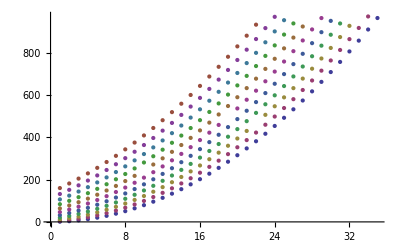

```mathematica
ListPlot[lsplot]
```

## Least Squares Fit

Ls are in the form {n,l}

```mathematica
PolyFit[lambdas_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Inverse[M].{Sum[lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]*lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]^2*lambdas[[i,2]],{i,1,Length[lambdas]}]};
Return[{a->res[[1]],b->res[[2]],c->res[[3]]}]
]
```

```mathematica
DeltaYs[lambdas_,fit_]:=Sqrt[1/(Length[lambdas]-3)Sum[(lambdas[[i,2]]-(a+b lambdas[[i,1]]+c lambdas[[i,1]]^2)/.fit)^2,{i,1,Length[lambdas]}]]
```

```mathematica
DeltaABCs[lambdas_,fit_,dy_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Sqrt[Sum[(Inverse[M].{1,
lambdas[[i,1]],
lambdas[[i,1]]^2}*dy)^2,{i,1,Length[lambdas]}]];
Return[res]
]
```

```mathematica
Fits[[1]]
```

{a→0.0578679,b→0.0517547,c→0.785389}

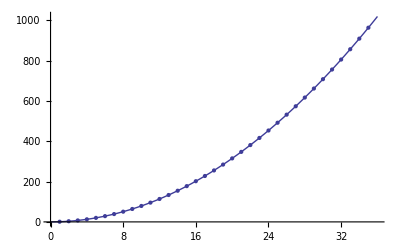

```mathematica
Show[Plot[(a + b x + c x^2)/.Fits[[1]],{x,0,36}],ListPlot[lsplot[[1]]]]
```

```mathematica
Fits=Table[PolyFit[lsplot[[i]]],{i,1,Length[lsplot]}];
```

```mathematica
dys=Table[DeltaYs[lsplot[[i]],Fits[[i]]],{i,1,Length[Fits]}];
```

```mathematica
l0[[1]]
```

{0.895295,0.0275888}

```mathematica
TableForm[Table[Join[{"l = "<>ToString[i-1]},Fits[[i]],{DeltaYs[lsplot[[i]],Fits[[i]]]}],{i,1,Length[Fits]}]]
```

l = 0 | a→0.0578679 | b→0.0517547 | c→0.785389 | 0.0018454
l = 1 | a→2.08389 | b→1.87181 | c→0.783359 | 0.061561
l = 2 | a→6.69367 | b→3.76342 | c→0.780961 | 0.100205
l = 3 | a→13.9713 | b→5.66987 | c→0.778668 | 0.126059
l = 4 | a→23.916 | b→7.58959 | c→0.776349 | 0.141452
l = 5 | a→36.5385 | b→9.51975 | c→0.774003 | 0.148965
l = 6 | a→51.8429 | b→11.4585 | c→0.771512 | 0.141571
l = 7 | a→69.8763 | b→13.3975 | c→0.769258 | 0.136714
l = 8 | a→90.6213 | b→15.3367 | c→0.767164 | 0.129699
l = 9 | a→114.081 | b→17.2771 | c→0.765162 | 0.12079
l = 10 | a→140.221 | b→19.2291 | c→0.762649 | 0.101198

```mathematica
dabcs=Table[DeltaABCs[lsplot[[i]],Fits[[i]],dys[[i]]],{i,1,Length[lsplot]}]
```

{{0.000991933,0.00012705,3.4233×10^-6},{0.0336319,0.00443055,0.000122796},{0.0569554,0.00800701,0.000234662},{0.0725534,0.0104523,0.000316912},{0.0829445,0.0123341,0.000386055},{0.0896912,0.0139121,0.000448679},{0.0881913,0.014648,0.000509933},{0.0870456,0.0148573,0.000534104},{0.0844883,0.0149742,0.000559067},{0.0805912,0.0148535,0.000576805},{0.0710914,0.0142391,0.000601176}}

```mathematica
dabcs//TableForm
```

0.000991933 | 0.00012705 | 3.4233×10^-6
0.0336319 | 0.00443055 | 0.000122796
0.0569554 | 0.00800701 | 0.000234662
0.0725534 | 0.0104523 | 0.000316912
0.0829445 | 0.0123341 | 0.000386055
0.0896912 | 0.0139121 | 0.000448679
0.0881913 | 0.014648 | 0.000509933
0.0870456 | 0.0148573 | 0.000534104
0.0844883 | 0.0149742 | 0.000559067
0.0805912 | 0.0148535 | 0.000576805
0.0710914 | 0.0142391 | 0.000601176

```mathematica
Fits[[11,3]]
```

c→0.762649

```mathematica
(c/.{Fits[[11,3]]})+dabcs[[11,3]]
```

0.763251

```mathematica
as=Table[{i-1,a/.Fits[[i,1]]},{i,1,Length[Fits]}]
```

{{0,0.0578679},{1,2.08389},{2,6.69367},{3,13.9713},{4,23.916},{5,36.5385},{6,51.8429},{7,69.8763},{8,90.6213},{9,114.081},{10,140.221}}

```mathematica
aserr=Table[{{i-1,a/.Fits[[i,1]]},ErrorBar[dabcs[[i,1]]]},{i,1,Length[Fits]}];
```

```mathematica
bs=Table[{i-1,b/.Fits[[i,2]]},{i,1,Length[Fits]}]
```

{{0,0.0517547},{1,1.87181},{2,3.76342},{3,5.66987},{4,7.58959},{5,9.51975},{6,11.4585},{7,13.3975},{8,15.3367},{9,17.2771},{10,19.2291}}

```mathematica
bserr=Table[{{i-1,b/.Fits[[i,2]]},ErrorBar[dabcs[[i,2]]]},{i,1,Length[Fits]}];
```

```mathematica
cs=Table[{i-1,c/.Fits[[i,3]]},{i,1,Length[Fits]}]
```

{{0,0.785389},{1,0.783359},{2,0.780961},{3,0.778668},{4,0.776349},{5,0.774003},{6,0.771512},{7,0.769258},{8,0.767164},{9,0.765162},{10,0.762649}}

```mathematica
cserr=Table[{{i-1,c/.Fits[[i,3]]},ErrorBar[dabcs[[i,3]]]},{i,1,Length[Fits]}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

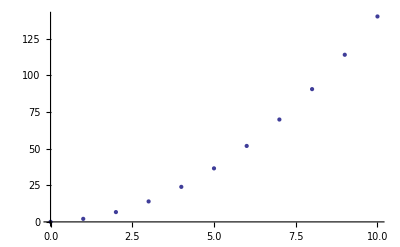

```mathematica
ErrorListPlot[aserr]
```

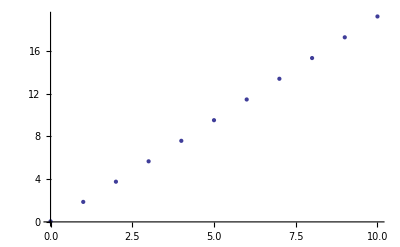

```mathematica
ErrorListPlot[bserr]
```

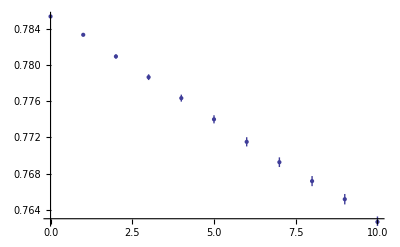

```mathematica
ErrorListPlot[cserr]
```